```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/y/Nutstore Files/1Project/1Qdia/code/7BrickWall_appendix/Nq5_block_var_tmin2/Res

```mathematica
lossPm5 = Import["lossPb5.0.txt","Data"];
lossPm10 = Import["lossPb10.0.txt","Data"];
lossPm15 = Import["lossPb15.0.txt","Data"];
lossPm20= Import["lossPb20.0.txt","Data"];
lossPm25 = Import["lossPb25.0.txt","Data"];
lossPm30 = Import["lossPb30.0.txt","Data"];
lossPm35 = Import["lossPb35.0.txt","Data"];
lossPm40 = Import["lossPb40.0.txt","Data"];
lossPm45 = Import["lossPb45.0.txt","Data"];
lossPm50 = Import["lossPb50.0.txt","Data"];
lossPm55= Import["lossPb55.0.txt","Data"];
lossPm60 = Import["lossPb60.0.txt","Data"];
lossPm65 = Import["lossPb65.0.txt","Data"];
lossPm70 = Import["lossPb70.0.txt","Data"];
lossPm75 = Import["lossPb75.0.txt","Data"];
```

```mathematica
mSet = Range[5,75,5];
lossSet={lossPm5⟦-1,4⟧,lossPm10⟦-1,4⟧,lossPm15⟦-1,4⟧,lossPm20⟦-1,4⟧,lossPm25⟦-1,4⟧,lossPm30⟦-1,4⟧,lossPm35⟦-1,4⟧,lossPm40⟦-1,4⟧,lossPm45⟦-1,4⟧,lossPm50⟦-1,4⟧,lossPm55⟦-1,4⟧,lossPm60⟦-1,4⟧,lossPm65⟦-1,4⟧,lossPm70⟦-1,4⟧,lossPm75⟦-1,4⟧};
```

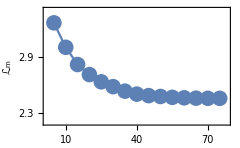

```mathematica
Figlossm=ListLinePlot[Transpose@{mSet,lossSet},PlotRange->{{2,78},{2.2,3.4}},Frame->True,Axes->None,FrameStyle->Thickness[0.006],FrameTicksStyle->Directive[Black,Bold,12],PlotMarkers->Style["●",FontSize->16],FrameLabel->{Style["m",Directive[Large],Black,FontSize->14],Style["ℒ_m",Italic,Directive[Large],Black,FontSize->16]},RotateLabel->False,FrameTicks->{{{2.3,2.6,2.9,3.2},None},{{10,20,30,40,50,60,70},None}},ImageSize->{240,160}]
```

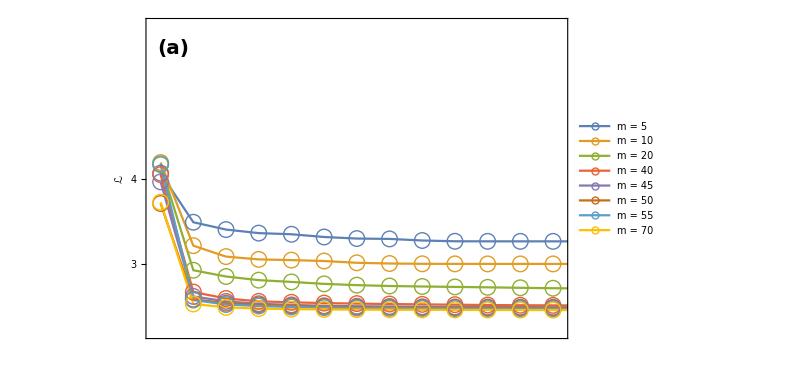
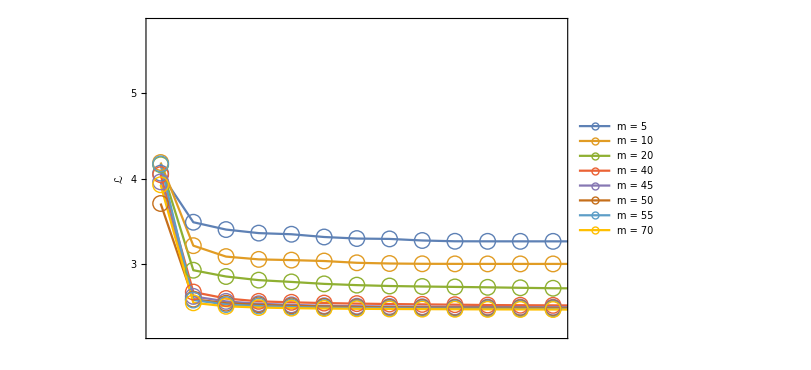

```mathematica
FiglossL1=ListLinePlot[{lossPm5⟦All,{2,4}⟧,lossPm10⟦All,{2,4}⟧,lossPm20⟦All,{2,4}⟧,lossPm40⟦All,{2,4}⟧,lossPm45⟦All,{2,4}⟧,lossPm50⟦All,{2,4}⟧,lossPm55⟦All,{2,4}⟧,lossPm70⟦All,{2,4}⟧},PlotRange->{{-50,3050},{2.2,5.8}},FrameLabel->{None,Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->Style["○",FontSize->16],
FrameTicks->{{{{0,"0.0"},{2.0,"2"},1,3,4},None},{None,None}},
PlotLegends->Placed[{Style["m = 5",Bold,FontSize->14],Style["m = 10",Bold,FontSize->14],Style["m = 20",Bold,FontSize->14],Style["m = 40",Bold,FontSize->14],Style["m = 45",Bold,FontSize->14],Style["m = 50",Bold,FontSize->14],Style["m = 55",Bold,FontSize->14],Style["m = 70",Bold,FontSize->14]},{0.26,0.74}],
ImageSize->{600,291},ImagePadding->{{80,80},{1,10}},Epilog->Inset[Style["(a)",Bold,FontSize->20],{100,5.52}]];
FiglossL2=ListLinePlot[{lossPm5⟦All,{2,4}⟧,lossPm10⟦All,{2,4}⟧,lossPm20⟦All,{2,4}⟧,lossPm40⟦All,{2,4}⟧,lossPm45⟦All,{2,4}⟧,lossPm50⟦All,{2,4}⟧,lossPm55⟦All,{2,4}⟧,lossPm60⟦All,{2,4}⟧},PlotRange->{{-50,3050},{2.2,5.8}},FrameLabel->{None,Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->Style["○",FontSize->16],
FrameTicks->{{{{0,"0.0"},{2.0,"2"},1,3,4,5},None},{None,None}},
PlotLegends->Placed[{Style["m = 5",Bold,FontSize->14],Style["m = 10",Bold,FontSize->14],Style["m = 20",Bold,FontSize->14],Style["m = 40",Bold,FontSize->14],Style["m = 45",Bold,FontSize->14],Style["m = 50",Bold,FontSize->14],Style["m = 55",Bold,FontSize->14],Style["m = 70",Bold,FontSize->14]},{0.26,0.74}],
ImageSize->{600,291},ImagePadding->{{80,80},{1,10}},Epilog->Inset[Figlossm,{2220,4.78}]];
Figa = Overlay[{FiglossL1,FiglossL2}]
```

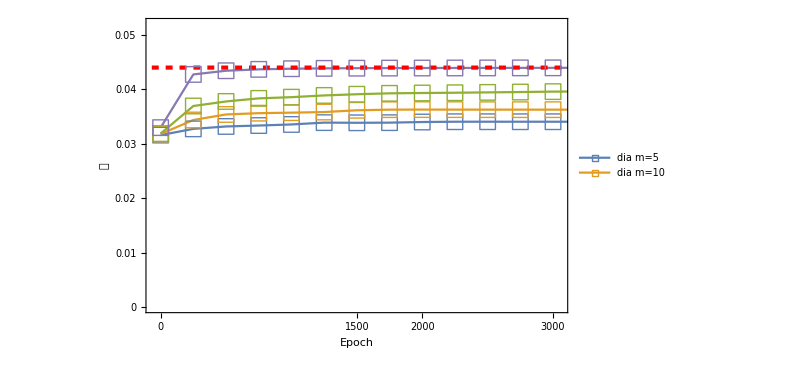
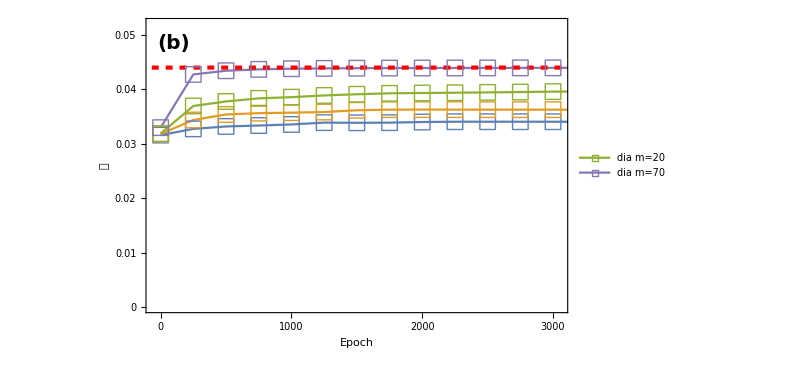

```mathematica
FigDiaL1=ListLinePlot[{lossPm5⟦All,{2,6}⟧,lossPm10⟦All,{2,6}⟧,lossPm20⟦All,{2,6}⟧,lossPm70⟦All,{2,6}⟧+1000,lossPm70⟦All,{2,6}⟧},
PlotRange->{{-50,3050},{0,0.052}},FrameLabel->{{Style["𝒟",Italic,Directive[Large],Black,FontSize->20],None},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{lossPm5⟦1,8⟧}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["□",FontSize->16]},
FrameTicks->{{{0,0.01,0.02,0.03,0.04,0.05},None},{{0,1000,2000,500,1500,2500,3000,4000,5000},None}},
PlotLegends->Placed[{Style["dia m=5",Bold,FontSize->14],Style["dia m=10",Bold,FontSize->14],None,None,None},{0.13,0.45}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}}];
FigDiaL2=ListLinePlot[{lossPm5⟦All,{2,6}⟧,lossPm10⟦All,{2,6}⟧,lossPm20⟦All,{2,6}⟧,lossPm70⟦All,{2,6}⟧+1000,lossPm70⟦All,{2,6}⟧},
PlotRange->{{-50,3050},{0,0.052}},FrameLabel->{{Style["𝒟",Italic,Directive[Large],Black,FontSize->20],None},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{lossPm5⟦1,8⟧}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["□",FontSize->16]},
FrameTicks->{{{0,0.01,0.02,0.03,0.04,0.05},None},{{0,1000,2000,3000,4000,5000},None}},
PlotLegends->Placed[{None,None,Style["dia m=20",Bold,FontSize->14],None,Style["dia m=70",Bold,FontSize->14]},{0.35,0.45}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}},Epilog->Inset[Style["(b)",Bold,FontSize->20],{100,0.0485}]];
FigDia=Overlay[{FigDiaL1,FigDiaL2}]
```

```mathematica
FigoffDL1=ListLinePlot[{lossPm5⟦All,{2,10}⟧,lossPm10⟦All,{2,10}⟧,lossPm20⟦All,{2,10}⟧,lossPm70⟦All,{2,10}⟧+1000,lossPm70⟦All,{2,10}⟧},PlotRange->{{-50,3050},{-0.0006,0.012}},FrameLabel->{{None,None},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[White,Bold,16],PlotMarkers->{Style["△",FontSize->16]},
FrameTicks->{{None,{{0.011,Style["  ×10^-3",Black]}}},{{0,1000,2000,3000,4000,5000},None}},
PlotLegends->Placed[{None,None,None},{0.75,0.45}],
Epilog->Inset[Style["(b)",Bold,FontSize->20],{0.95,0.22}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}}];
FigoffDL2=ListLinePlot[{lossPm5⟦All,{2,10}⟧,lossPm10⟦All,{2,10}⟧,lossPm20⟦All,{2,10}⟧,lossPm70⟦All,{2,10}⟧+1000,lossPm70⟦All,{2,10}⟧},PlotRange->{{-50,3050},{-0.0006,0.012}},FrameLabel->{{None,Style["(|ρ_(('_(off-dia))_)|)^(—————–)",Italic,Directive[Large],Black,FontSize->20]},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["△",FontSize->16]},
FrameTicks->{{None,{0,{0.003,"3"},{0.006,"6"},{0.009,"9"}}},{{0,1000,2000,3000,4000,5000},None}},
PlotLegends->Placed[{None,None,Style["off-dia m=20",Bold,FontSize->14],None,Style["off-dia m=70",Bold,FontSize->14]},{0.85,0.455}],
Epilog->Inset[Style["(b)",Bold,FontSize->20],{0.95,0.22}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}}];
FigoffDL3=ListLinePlot[{lossPm5⟦All,{2,10}⟧,lossPm10⟦All,{2,10}⟧,lossPm20⟦All,{2,10}⟧,lossPm70⟦All,{2,10}⟧+1000,lossPm70⟦All,{2,10}⟧},PlotRange->{{-50,3050},{-0.0006,0.012}},FrameLabel->{{None,Style["(|ρ_(('_(off-dia))_)|)^(—————–)",Italic,Directive[Large],Black,FontSize->20]},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["△",FontSize->16]},
FrameTicks->{{None,{0,{0.003,"3"},{0.006,"6"},{0.009,"9"}}},{{0,500,1500,2500,1000,2000,3000,4000,5000},None}},
PlotLegends->Placed[{Style["off-dia m=5",Bold,FontSize->14],Style["off-dia m=10",Bold,FontSize->14],None,None,None},{0.59,0.455}],
Epilog->Inset[Style["(b)",Bold,FontSize->20],{0.95,0.22}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}}];
```

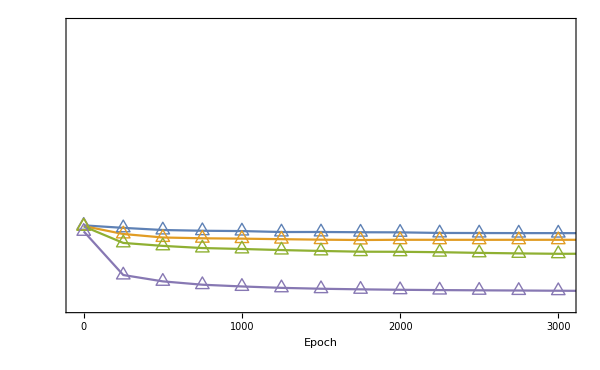
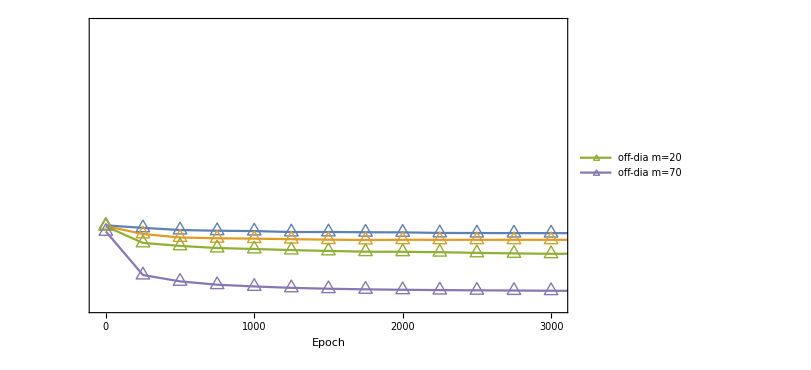
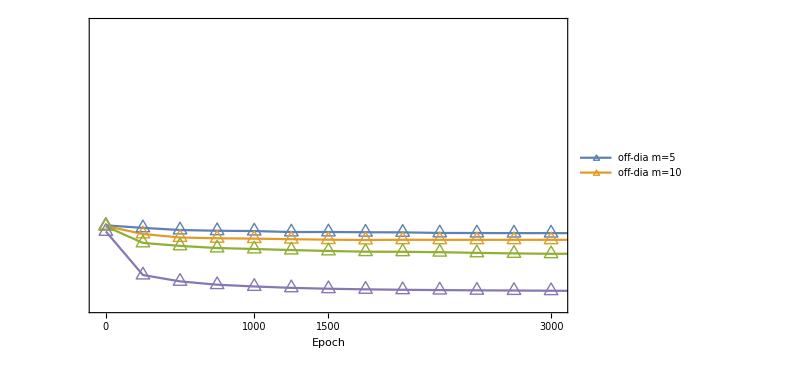

```mathematica
FigoffD= Overlay[{FigoffDL1,FigoffDL2,FigoffDL3}]
```

```mathematica
Figb=Overlay[{FigDia,FigoffD}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Fig4=Grid[{{Figa},{Figb}},Spacings->{Automatic, -0.8}]
```

-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["Fig4.pdf",Fig4]
```

Fig4.pdf